# 2-loop electron self-enegery with IREG

## Rainbow Diagram - Massless Case

## FeynCalc with FeynArts and TARCER

```mathematica
(*Load FeynCalc with FeynArts and the package TARCER*)
```

```mathematica
description="Electron self-energy at 2-loop with IREG-Rainbow diagram";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"TARCER","FeynArts"};
Get["FeynCalc`"]
$FAVerbose=0;
FCCheckVersion[9,3,0];
$Comment=True;
Off[General::"spell"];
Off[General::"spell1"];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

TARCER 2.0, for more information see the accompanying publication. If you use TARCER in your research, please cite

• R. Mertig and R. Scharf, Comput. Phys. Commun., 111, 265-273, 1998, arXiv:hep-ph/9801383

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

## Fermion to Fermion process defined

```mathematica
ClearProcess[];
Processee={F[2,{1}]}->{F[2,{1}]};
SetOptions[InsertFields,InsertionLevel->{Particles},Model->FileNameJoin[{"QED","QED"}],GenericModel->FileNameJoin[{"QED","QED"}],ExcludeParticles->{F[2,{2|3}]}];
```

## Topology Generation with FeynArts

```mathematica
(*Topology creation with FeynArts function CreateTopologies[]. 1PI 2-loop topology for a 1->1 fermion (F[2,{1}]) process is generated. Default options for FeynArts function InsertFields[] are set*)
```

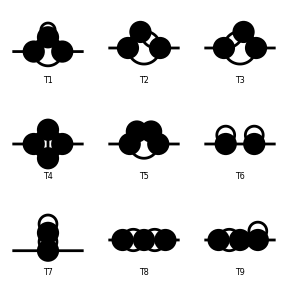

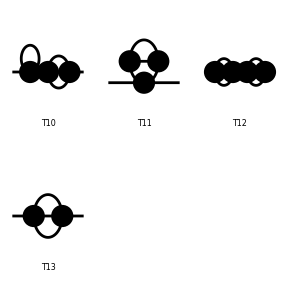

FeynArtsGraphics(1→1)(([T1] | [T2] | [T3]
[T4] | [T5] | [T6]
[T7] | [T8] | [T9]),([T10] | [T11] | [T12]
[T13] | Null | Null
Null | Null | Null))

```mathematica
Topologiesfermions=CreateTopologies[2,1->1,ExcludeTopologies->{Tadpoles}];
Paint[Topologiesfermions]
```

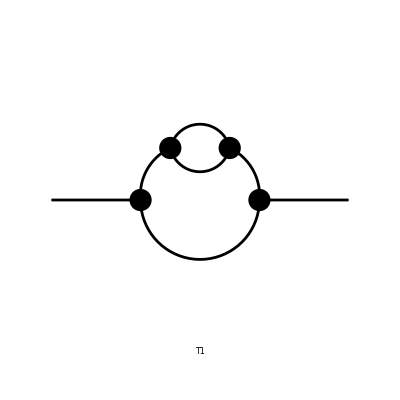

FeynArtsGraphics(1→1)(([T1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
bubbletopologies=Take[Topologiesfermions,{5}];
Paint[bubbletopologies]
```

## Rainbow counter-term 1-loop topology

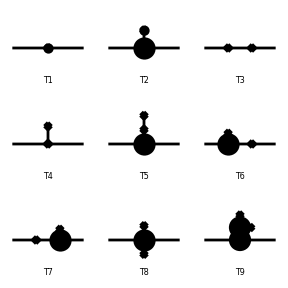

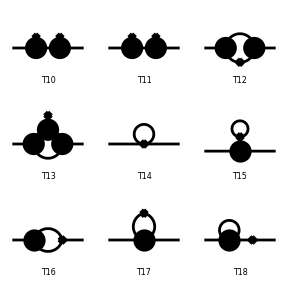

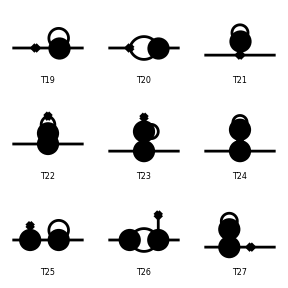

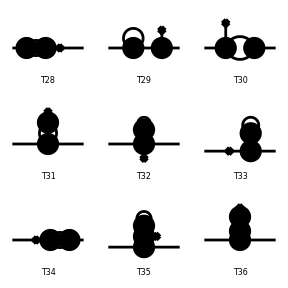

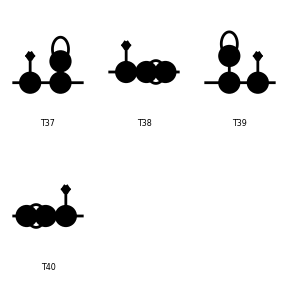

FeynArtsGraphics(1→1)(([T1] | [T2] | [T3]
[T4] | [T5] | [T6]
[T7] | [T8] | [T9]),([T10] | [T11] | [T12]
[T13] | [T14] | [T15]
[T16] | [T17] | [T18]),([T19] | [T20] | [T21]
[T22] | [T23] | [T24]
[T25] | [T26] | [T27]),([T28] | [T29] | [T30]
[T31] | [T32] | [T33]
[T34] | [T35] | [T36]),([T37] | [T38] | [T39]
[T40] | Null | Null
Null | Null | Null))

```mathematica
Topology1LoopFermionicSelfEnergyCorrection=CreateCTTopologies[2,1->1];
Paint[Topology1LoopFermionicSelfEnergyCorrection]
```

```mathematica
CorrectionForRainbowDiagramTopology=Take[Topology1LoopFermionicSelfEnergyCorrection,{12}];
```

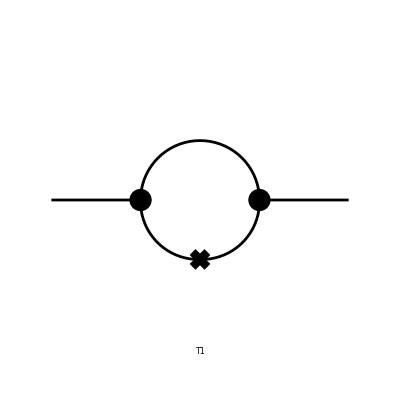

FeynArtsGraphics(1→1)(([T1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
Paint[CorrectionForRainbowDiagramTopology]
```

## Diagram generation with fields

```mathematica
(*We substitute the propagators and external fields from QED in previous selected topology*)
```

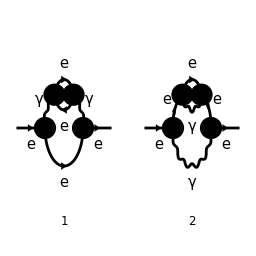

FeynArtsGraphics()(([1] | [2]))

```mathematica
bubbleWITHfields=InsertFields[bubbletopologies,Processee,ExcludeParticles->{S[_],V[2|3],(S|U)[_],F[3|4],F[2,{2|3}]}];
Paint[bubbleWITHfields,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}]
```

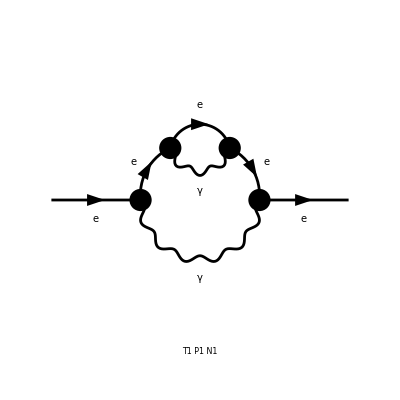

FeynArtsGraphics({e}→{e})(([T1 P1 N1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
therainbowdiagram=DiagramExtract[bubbleWITHfields,2];
Paint[therainbowdiagram]
```

## Insertion of fields in counter-term’s topologies

Rainbow counter-term with fields

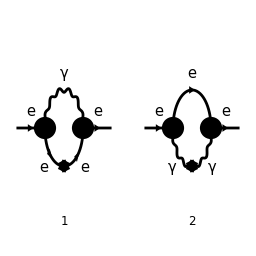

```mathematica
BubbleCounterTerms=InsertFields[CorrectionForRainbowDiagramTopology,Processee,ExcludeParticles->{S[_],V[2|3],(S|U)[_],F[3|4],F[2,{2|3}]}];
Paint[BubbleCounterTerms,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

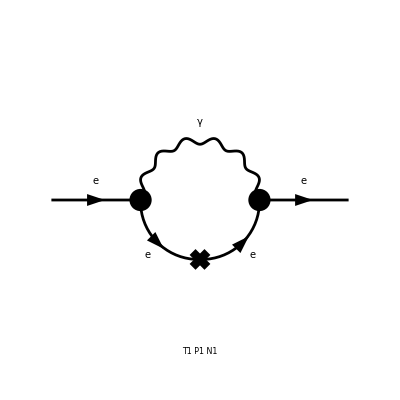

FeynArtsGraphics({e}→{e})(([T1 P1 N1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
RainbowDiagramCounterTerm=DiagramExtract[BubbleCounterTerms,{1}];
Paint[RainbowDiagramCounterTerm]
```

## Amplitude (no regularized)

```mathematica
(*Amplitude is generated in FeynArts with function CreateFeynAmp[]. This expression is later conver to FeynCalc using FCFAConvert[]. Feynman gauge Subscript[ξ, g]=1 is chose later*)
```

```mathematica
FAamplElectronB=CreateFeynAmp[therainbowdiagram,Truncated->True,GaugeRules->{},PreFactor->1];
```

### In 4-dim (for IREG integrals)

```mathematica
(*Notice that we set in FCFAConvert options that ChangeDimensions->4*)
```

```mathematica
(*As this notebook is just to revised the massless case, the old mass scenario is hide with ";". Not relevant for what I wanna test today*)
```

```mathematica
convertamplElectronB2=FCFAConvert[FAamplElectronB,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{l,k},LorentzIndexNames->{μ,ν,α,β},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,DropSumOver->True,Contract->True];
```

```mathematica
(*We work now in Feynman gauge*)
```

```mathematica
FeynmangaugeamplElectronB2=convertamplElectronB2/. GaugeXi[V[1]] -> 1
```

(ⅈ e^4 (γ̄)^ν.(γ̄·(p̄-l̄)+m_e).(γ̄)^β.(m_e-γ̄·k̄).(γ̄)^β.(γ̄·(p̄-l̄)+m_e).(γ̄)^ν)/((l̄)^2.((k̄)^2-m_e^2).((l̄-p̄)^2-m_e^2)^2.(k̄-l̄+p̄)^2)

```mathematica
AlgebraDiracElectronB2A=DiracSimplify[FeynmangaugeamplElectronB2];
```

```mathematica
(*It is hard to notice at first sight, but even using DiracSimplify, still there are some simplification we can still do with the matrices. So using DiracSimplify again will be necessary... sometimes*)
```

```mathematica
AlgebraDiracElectronC2A=DiracSimplify[AlgebraDiracElectronB2A];
```

```mathematica
(*... it didn't change much*)
```

```mathematica
FinalElectronBAmpforIREG=Simplify[AlgebraDiracElectronC2A];
```

## Integrals

### Integrals-IREG

```mathematica
{irrelevantIREG,loops,THEUNIQUEIREGINTEGRALS}=FCLoopExtract[FinalElectronBAmpforIREG,{l,k},loopHeadIREG];
IREGINTEGRALSQB=THEUNIQUEIREGINTEGRALS/.loopHeadIREG->Identity;
```

## Working in the massless regime

```mathematica
(*To compute the counterterm of the electron field, we set the mass zero in the amplitude before doing the simplification of Dirac matrices*)
```

```mathematica
ElectronB2massless=FeynmangaugeamplElectronB2//.SMP["m_e"]->0
```

(ⅈ e^4 (γ̄)^ν.(γ̄·(p̄-l̄)).(γ̄)^β.(-(γ̄·k̄)).(γ̄)^β.(γ̄·(p̄-l̄)).(γ̄)^ν)/((l̄)^2.(k̄)^2.((l̄-p̄)^2)^2.(k̄-l̄+p̄)^2)

```mathematica
(*First, we want to change the printed output to a an easy-to-read form. $PrePrint=FeynCalcForm forces displaying everything after applying FeynCalcForm*)
```

```mathematica
$PrePrint=FeynCalcForm;
```

```mathematica
SetOptions[$FrontEndSession,Evaluate[(Options[$FrontEndSession,"CommonDefaultFormatTypes"]/.("Output"->_)->("Output"->OutputForm))[[1]]]];
```

```mathematica
Print[ElectronB2massless]
```

I DiracGamma[LorentzIndex[ν]] . DiracGamma[Momentum[-l + p]] . 
 
      DiracGamma[LorentzIndex[β]] . (-DiracGamma[Momentum[k]]) . 
 
      DiracGamma[LorentzIndex[β]] . DiracGamma[Momentum[-l + p]] . 
 
      DiracGamma[LorentzIndex[ν]] 
 
     FeynAmpDenominator[PropagatorDenominator[Momentum[l], 0], 
 
      PropagatorDenominator[Momentum[k], 0], 
 
      PropagatorDenominator[Momentum[l - p], 0], 
 
      PropagatorDenominator[Momentum[l - p], 0], 
 
                                                           4
      PropagatorDenominator[Momentum[k - l + p], 0]] SMP[e]

```mathematica
(*In order to change to the normal (internal) Mathematica OutputForm, we do:($PrePrint=.)*)
```

```mathematica
$PrePrint=.;
```

```mathematica
SetOptions[$FrontEndSession,Evaluate[(Options[$FrontEndSession,"CommonDefaultFormatTypes"]/.("Output"->_)->("Output"->TraditionalForm))[[1]]]];
```

```mathematica
(*Just to check that all it's fine, let us print again the amplitude we are interested*)
```

```mathematica
Print[ElectronB2massless]
```

(ⅈ e^4 (γ̄)^ν.(γ̄·(p̄-l̄)).(γ̄)^β.(-(γ̄·k̄)).(γ̄)^β.(γ̄·(p̄-l̄)).(γ̄)^ν)/((l̄)^2.(k̄)^2.((l̄-p̄)^2)^2.(k̄-l̄+p̄)^2)

```mathematica
(*Let's define then the general shift l->l+p for each part*)
```

```mathematica
ShiftA={Momentum[l]->Momentum[l+p]};
```

```mathematica
ShiftB={DiracGamma[Momentum[-l+p]]->(-DiracGamma[Momentum[l]])};
```

```mathematica
ShiftC={Momentum[l-p]->Momentum[l]};
```

```mathematica
ShiftD={Momentum[k-l+p]->Momentum[k-l]};
```

```mathematica
(*Sadly, in a define the general shift l->l+p in separated parts because if not I have conflicts with the substitution after*)
```

```mathematica
ElectronB2masslessSHIFA=ElectronB2massless//.ShiftA;
ElectronB2masslessSHIFB=ElectronB2masslessSHIFA//.ShiftB;
ElectronB2masslessSHIFC=ElectronB2masslessSHIFB//.ShiftC;
ElectronB2masslessSHIFD=ElectronB2masslessSHIFC//.ShiftD
```

(ⅈ e^4 (γ̄)^ν.(-(γ̄·l̄)).(γ̄)^β.(-(γ̄·k̄)).(γ̄)^β.(-(γ̄·l̄)).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
AlgebraDiracElectronB2Amassless=DiracSimplify[ElectronB2masslessSHIFD]
```

(4 ⅈ e^4 (l̄)^2 γ̄·k̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-(8 ⅈ e^4 (k̄·l̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
AlgebraDiracElectronC2Amassless=DiracSimplify[AlgebraDiracElectronB2Amassless]
```

(4 ⅈ e^4 (l̄)^2 γ̄·k̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-(8 ⅈ e^4 (k̄·l̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

### Integrals for massless amplitude

```mathematica
{irrelevantmasslessIREG,loopsmassless,THEUNIQUEIREGINTEGRALSmassless}=FCLoopExtract[AlgebraDiracElectronC2Amassless,{l,k},loopHeadIREGmassless];
IREGINTEGRALSEBmassless=THEUNIQUEIREGINTEGRALSmassless/.loopHeadIREGmassless->Identity
```

{((k̄·l̄) γ̄·l̄)/(((l̄)^2)^2.(k̄)^2.(k̄-l̄)^2.(l̄+p̄)^2),((l̄)^2 γ̄·k̄)/(((l̄)^2)^2.(k̄)^2.(k̄-l̄)^2.(l̄+p̄)^2)}

### Rainbow C.T and integrals

```mathematica
FAamplrainbowCT=CreateFeynAmp[RainbowDiagramCounterTerm,Truncated->True,GaugeRules->{},PreFactor->1];
```

```mathematica
convertamplRainbowCT=FCFAConvert[FAamplrainbowCT,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{l},LorentzIndexNames->{μ,ν,α,β},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,DropSumOver->True,Contract->True,FinalSubstitutions->{Zm->SMP["Z_m"],Zpsi->SMP["Z_psi"],GaugeXi[V[1]]->1}];
convertamplRainbowCTmassless=convertamplRainbowCT//.SMP["m_e"]->0
```

-(ⅈ e^2 (γ̄)^ν.(-(γ̄·l̄)).(-ⅈ (Z_ψ-1) γ̄·l̄).(-(γ̄·l̄)).(γ̄)^ν)/(((l̄)^2)^2.(l̄+p̄)^2)

```mathematica
AlgebraDiracmasslessCTRainbow1=DiracSimplify[convertamplRainbowCTmassless];
AlgebraDiracmasslessCTRainbow2=DiracSimplify[AlgebraDiracmasslessCTRainbow1]
```

(2 e^2 (l̄)^2 Z_ψ γ̄·l̄)/(((l̄)^2)^2.(l̄+p̄)^2)-(2 e^2 (l̄)^2 γ̄·l̄)/(((l̄)^2)^2.(l̄+p̄)^2)

```mathematica
{irrelevantmasslessIREGCTRAINBOW,loopsmasslessCTRAINBOW,THEUNIQUEIREGINTEGRALSmasslessCTRAINBOW}=FCLoopExtract[AlgebraDiracmasslessCTRainbow2,{l},loopHeadIREGmasslessCTRAINBOW];
IREGINTEGRALSEBmasslessCTRAINBOW=THEUNIQUEIREGINTEGRALSmasslessCTRAINBOW/.loopHeadIREGmasslessCTRAINBOW->Identity
```

{((l̄)^2 γ̄·l̄)/(((l̄)^2)^2.(l̄+p̄)^2)}

## Replacements

### The full form of the amplitude (massless case)

```mathematica
(*First, we want to change the printed output to a an easy-to-read form. $PrePrint=FeynCalcForm forces displaying everything after applying FeynCalcForm*)
```

```mathematica
$PrePrint=FeynCalcForm;
```

```mathematica
SetOptions[$FrontEndSession,Evaluate[(Options[$FrontEndSession,"CommonDefaultFormatTypes"]/.("Output"->_)->("Output"->OutputForm))[[1]]]];
```

```mathematica
Print[AlgebraDiracElectronC2Amassless]
```

(-8 I) DiracGamma[Momentum[l]] FeynAmpDenominator[PropagatorDenominator[
 
        Momentum[l + p], 0], PropagatorDenominator[Momentum[k], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[Momentum[k - l], 0]] Pair[Momentum[k], Momentum[l]] 
 
            4
      SMP[e]  + (4 I) DiracGamma[Momentum[k]] 
 
      FeynAmpDenominator[PropagatorDenominator[Momentum[l + p], 0], 
 
       PropagatorDenominator[Momentum[k], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[Momentum[k - l], 0]] Pair[Momentum[l], Momentum[l]] 
 
            4
      SMP[e]

```mathematica
(*In order to change to the normal (internal) Mathematica OutputForm, we do:($PrePrint=.)*)
```

```mathematica
$PrePrint=.;
```

```mathematica
SetOptions[$FrontEndSession,Evaluate[(Options[$FrontEndSession,"CommonDefaultFormatTypes"]/.("Output"->_)->("Output"->TraditionalForm))[[1]]]];
```

```mathematica
Print[AlgebraDiracElectronC2Amassless]
```

(4 ⅈ e^4 (l̄)^2 γ̄·k̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-(8 ⅈ e^4 (k̄·l̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

### Integral results (massless case)

```mathematica
(*What I computed by hand*)
```

```mathematica
D2Replace=-DiracGamma[Momentum[p]]/4 Ilogλ2^2+(b*DiracGamma[Momentum[p]])/4 Ilogλ2*Log[-p^2/λ^2]-(b*DiracGamma[Momentum[p]])/2 Ilogλ2+(b*DiracGamma[Momentum[p]])/4 Ilog2λ2+(b*DiracGamma[Momentum[p]])/8 Ilogλ2-(b*DiracGamma[Momentum[p]])/2 Ilogλ2
```

1/4 b Ilog2λ2 γ̄·p̄+1/4 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄-7/8 b Ilogλ2 γ̄·p̄-1/4 Ilogλ2^2 γ̄·p̄

```mathematica
TheTrueFReplace=-DiracGamma[Momentum[p]]/4*Ilogλ2^2+DiracGamma[Momentum[p]]/4*b*Ilogλ2*Log[-p^2/λ^2]-DiracGamma[Momentum[p]]/2*b*Ilogλ2+DiracGamma[Momentum[p]]/4*b*Ilog2λ2+DiracGamma[Momentum[p]]/8*b*Ilogλ2-DiracGamma[Momentum[p]]/2*b*Ilogλ2
```

1/4 b Ilog2λ2 γ̄·p̄+1/4 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄-7/8 b Ilogλ2 γ̄·p̄-1/4 Ilogλ2^2 γ̄·p̄

### Integral list (massless case)

```mathematica
(*To use it after in the replacemetns*)
```

```mathematica
TermD2=DiracGamma[Momentum[l]] FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[k-l],0]] Pair[Momentum[k],Momentum[l]]
```

((k̄·l̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
TermTheTrueF=DiracGamma[Momentum[k]]FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[k-l],0]] Pair[Momentum[l],Momentum[l]]
```

((l̄)^2 γ̄·k̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

### Evaluation of the integrals in the rainbow C.T

```mathematica
(*As before, the integrals were computed by hand. All are proportional to p slash, so we are writting that already for do after the replacement rule*)
```

```mathematica
(*To use it after in the replacemetns*)
```

```mathematica
CTBTerm=DiracGamma[Momentum[l]] FeynAmpDenominator[PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l+p],0]] Pair[Momentum[l],Momentum[l]]
```

((l̄)^2 γ̄·l̄)/(((l̄)^2)^2.(l̄+p̄)^2)

```mathematica
(*What I computed by hand*)
```

```mathematica
CTBReplace=-DiracGamma[Momentum[p]]/2*(Ilogλ2-b*Log[-p^2/λ^2]+2*b)
```

-1/2 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)

### Substitution rule for Mathematica

```mathematica
SubRule={TermD2->D2Replace,TermTheTrueF->TheTrueFReplace}
```

{((k̄·l̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)→1/4 b Ilog2λ2 γ̄·p̄+1/4 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄-7/8 b Ilogλ2 γ̄·p̄-1/4 Ilogλ2^2 γ̄·p̄,((l̄)^2 γ̄·k̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)→1/4 b Ilog2λ2 γ̄·p̄+1/4 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄-7/8 b Ilogλ2 γ̄·p̄-1/4 Ilogλ2^2 γ̄·p̄}

```mathematica
(*Substitution rule for the rainbow C.T*)
```

```mathematica
SubRuleforRainbowCT={CTBTerm->CTBReplace};
```

### Regulated Amplitud with IREG (massless case)

```mathematica
RegulatedAmplitude=AlgebraDiracElectronC2Amassless//.SubRule
```

-4 ⅈ e^4 (1/4 b Ilog2λ2 γ̄·p̄+1/4 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄-7/8 b Ilogλ2 γ̄·p̄-1/4 Ilogλ2^2 γ̄·p̄)

```mathematica
RegulatedRainbowAmplitudeIREG=Simplify[RegulatedAmplitude]
```

-1/2 ⅈ e^4 γ̄·p̄ (2 b Ilog2λ2+2 b Ilogλ2 log(-p^2/λ^2)-7 b Ilogλ2-2 Ilogλ2^2)

### The final rainbow C.T

```mathematica
RainbowCounterTermFinal=AlgebraDiracmasslessCTRainbow2//.SubRuleforRainbowCT
```

e^2 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)-e^2 Z_ψ γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)

```mathematica
(*The renormalization constant of the field for IREG*)
```

```mathematica
Z2=1+SMP["e"]^2*SMP["d_psi"]
```

e^2 δ_ψ+1

```mathematica
NewRuleCTRainbow={SMP["Z_psi"]->Z2};
```

```mathematica
RainbowCounterTermFinal2=RainbowCounterTermFinal//.NewRuleCTRainbow
```

e^2 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)-e^2 (e^2 δ_ψ+1) γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)

```mathematica
RainbowCounterTermFinal3=Simplify[RainbowCounterTermFinal2]
```

e^4 δ_ψ γ̄·p̄ (b log(-p^2/λ^2)-2 b-Ilogλ2)

## Removing the divergences (renormalization: regularized diagram+counter-term)

```mathematica
(*If everything is well, non-local terms should cancel*)
```

```mathematica
(*Before doing this, let's put some definitions for the counter-terms. All of them where taken for our Symmetry paper*)
```

```mathematica
CounterTermDeltaPsiQED=I*Ilogλ2
```

ⅈ Ilogλ2

```mathematica
(*Now, the substitution rules*)
```

```mathematica
RuleCTField={SMP["d_psi"]->CounterTermDeltaPsiQED};
```

```mathematica
(*Re-writting the counterterm*)
```

```mathematica
RainbowCounterTermFinal4=RainbowCounterTermFinal3//.RuleCTField
```

ⅈ e^4 Ilogλ2 γ̄·p̄ (b log(-p^2/λ^2)-2 b-Ilogλ2)

```mathematica
ChaveRainbow=RegulatedRainbowAmplitudeIREG+RainbowCounterTermFinal4
```

ⅈ e^4 Ilogλ2 γ̄·p̄ (b log(-p^2/λ^2)-2 b-Ilogλ2)-1/2 ⅈ e^4 γ̄·p̄ (2 b Ilog2λ2+2 b Ilogλ2 log(-p^2/λ^2)-7 b Ilogλ2-2 Ilogλ2^2)

```mathematica
ChaveRainbow2=Simplify[ChaveRainbow]
```

-1/2 ⅈ b e^4 (2 Ilog2λ2-3 Ilogλ2) γ̄·p̄